```mathematica
ClearAll["Global`*"];
If[Length[$FrontEnd]>0,SetDirectory[NotebookDirectory[]]];
<<Equiprobable-Returns-Functions.m;
```

```mathematica
𝓇1=0.02;
𝓇2=0.022;
𝓍 = 0.2;
Σ = 0.3;
ρ = 2;
uPlotTimes={};(* Used to keep track of the time it takes to produce the plots of utility *)
```

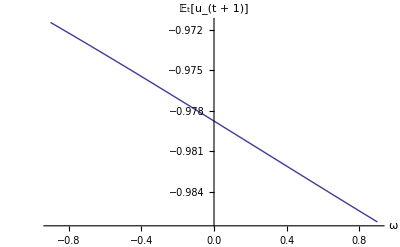

{{Equiprobable,0.285948}}

```mathematica
ϛ = 0.5;
𝔼uEquiSetup[NumOfPoints=15];
Print[AppendTo[uPlotTimes,{"Equiprobable",First[Timing[Print[Plot[𝔼uEqui[ϛ, 𝓇1, 𝓇2, 𝓍,Σ,ω, ρ],{ω,-0.9,0.9}
,AxesLabel->{"ω","𝔼_t[u_(t + 1)]"}]]]]}]];
```

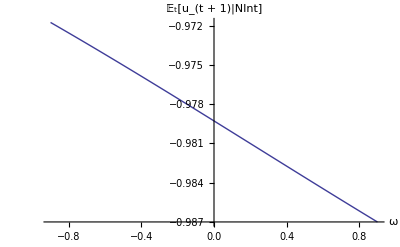

{{Equiprobable,0.285948},{Direct,10.6921}}

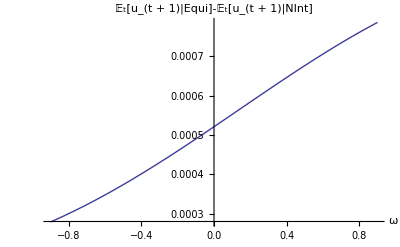

{{Equiprobable,0.285948},{Direct,10.6921},{Difference,10.7505}}

(Equiprobable | 0.285948
Direct | 10.6921
Difference | 10.7505)

```mathematica
Print[AppendTo[uPlotTimes,{"Direct",First[Timing[Print[
Plot[𝔼uNInt[ϛ, 𝓇1, 𝓇2,𝓍,Σ,ω, ρ],{ω,-0.9,0.9}
,AxesLabel->{"ω","𝔼_t[u_(t + 1)|NInt]"}]]]
]}]];

Print[AppendTo[uPlotTimes,{"Difference",First[Timing[Print[
Plot[𝔼uEqui[ϛ, 𝓇1, 𝓇2, 𝓍, Σ, ω, ρ]-𝔼uNInt[ϛ, 𝓇1, 𝓇2, 𝓍, Σ, ω, ρ],{ω,-0.9,0.9}
,AxesLabel->{"ω","𝔼_t[u_(t + 1)|Equi]-𝔼_t[u_(t + 1)|NInt]"}]]]
]}]];

Print[MatrixForm[uPlotTimes,TableHeadings->{None,"Method","Seconds"}]];
```

```mathematica
Clear[ϛ];
{ρMinPlot,ρMaxPlot}={1,3};ρGap=(ρMaxPlot-ρMinPlot);
ϛPlotTiming={};
ω=0.5;
```

```mathematica
Print[AppendTo[ϛPlotTiming,{"Direct",First[Timing[ϛPlotDirect = 
Plot[ϛOptDirect[𝓇1, 𝓇2, 𝓍,Σ,ω, ρ],{ρ,ρMinPlot,ρMaxPlot}
,PlotStyle->Black
,AxesLabel->{"ρ","ϛ"}
]]]}]];
ϛVals=Transpose[First@Cases[ϛPlotDirect,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛVals],Max[ϛVals]};
```

$Aborted

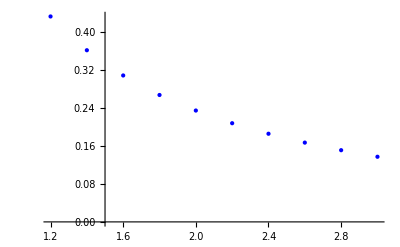

```mathematica
AppendTo[ϛPlotTiming,{"EquiprobableList",First[Timing[
NumPtsToUseForApprox=10;
ptsList= Table[ρMinPlot+ρGap(i/(NumPtsToUseForApprox)),{i,1,NumPtsToUseForApprox}]//N;
ϛOptEquiPts = Table[ϛOptEqui[𝓇1, 𝓇2, 𝓍, Σ, ω, ptsList[[i]]],{i,NumPtsToUseForApprox}];
Print[ϛPlotEquiList=ListPlot[Transpose[{ptsList,ϛOptEquiPts}],PlotStyle->Blue]]]]}];
```

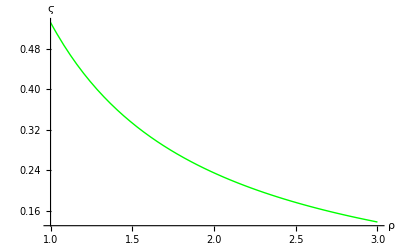

```mathematica
AppendTo[ϛPlotTiming,{"Equiprobable",First[Timing[Print[ϛPlotEqui = Plot[ϛOptEqui[𝓇1,𝓇2,𝓍,Σ,ω,ρ],{ρ,ρMinPlot,ρMaxPlot}
,PlotStyle->Green
,AxesLabel->{"ρ","ϛ"}
]]]]}];
ϛVals=Transpose[First@Cases[ϛPlotEqui,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛMin,Min[ϛVals]],Max[ϛMax,Max[ϛVals]]};
```

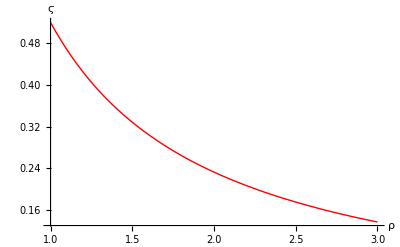

```mathematica
AppendTo[ϛPlotTiming,{"CVApprox",First[Timing[Print[
ϛPlotCVApprox = Plot[ϛOptCVApprox[𝓇1, 𝓇2, 𝓍, Σ, ω, ρ],{ρ,ρMinPlot,ρMaxPlot}
,PlotStyle->Red
,AxesLabel->{"ρ","ϛ"}
]]]]}];
ϛVals=Transpose[First@Cases[ϛPlotCVApprox,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛMin,Min[ϛVals]],Max[ϛMax,Max[ϛVals]]};
```

```mathematica
Print[Show[ϛPlotDirect,ϛPlotCVApprox,ϛPlotEqui,ϛPlotEquiList
,PlotLabel->Style["{Black, Red, Green}={Direct, CV, Equiprobable("<>ToString[NumOfPoints]<>")}",14,Black]
,PlotRange->{Automatic,{ϛMin-0.02,ϛMax+0.02}}]];
```

```mathematica
Print[MatrixForm[ϛPlotTiming,TableHeadings->{None,"Method","Seconds"}]];
```

(Direct | 753.125
EquiprobableList | 0.625834
Equiprobable | 4.79609
CVApprox | 0.004478)

```mathematica
(* Now examine results for ρ=2 and varying ω *)
```

```mathematica
ϛPlotTiming
```

{{EquiprobableList,0.578306},{Equiprobable,17.3155},{CVApprox,0.00935},{Direct,4333.14}}

```mathematica
Clear[ϛ,ω];
{ωMinPlot,ωMaxPlot}={-2.,2.};ωGap=(ωMaxPlot-ωMinPlot);
ϛPlotTiming={};
ρ=2.;
𝔼uEquiSetup[NumOfPoints=25];
```

```mathematica
Print[AppendTo[ϛPlotTiming,{"Direct",First[Timing[ϛPlotDirect = 
Plot[ϛOptDirect[𝓇1, 𝓇2, 𝓍, Σ, ω, ρ],{ω,ωMinPlot,ωMaxPlot}
,PlotStyle->Black
,AxesLabel->{"ω","ϛ"}
]]]}]];
ϛVals=Transpose[First@Cases[ϛPlotDirect,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛVals],Max[ϛVals]};
```

{{EquiprobableList,0.578306},{Equiprobable,17.3155},{CVApprox,0.00935},{Direct,4333.14}}

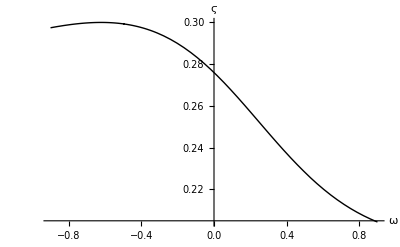

```mathematica
ϛPlotDirect
```

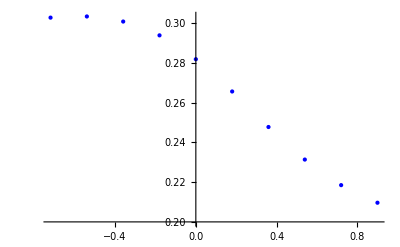

```mathematica
AppendTo[ϛPlotTiming,{"EquiprobableList",First[Timing[
NumPtsToUseForApprox=10;
ptsList= Table[ωMinPlot+ωGap(i/(NumPtsToUseForApprox)),{i,1,NumPtsToUseForApprox}]//N;
ϛOptEquiPts = Table[ϛOptEqui[𝓇1, 𝓇2, 𝓍, Σ, ptsList[[i]], ρ],{i,NumPtsToUseForApprox}];
Print[ϛPlotEquiList=ListPlot[Transpose[{ptsList,ϛOptEquiPts}],PlotStyle->Blue]]]]}];
```

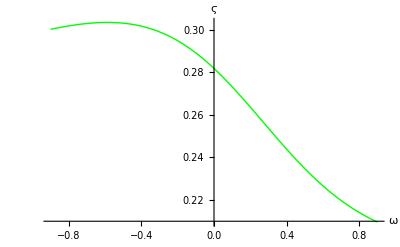

```mathematica
AppendTo[ϛPlotTiming,{"Equiprobable",First[Timing[Print[ϛPlotEqui = Plot[ϛOptEqui[𝓇1,𝓇2,𝓍,Σ,ω,ρ],{ω,ωMinPlot,ωMaxPlot}
,PlotStyle->Green
,AxesLabel->{"ω","ϛ"}
]]]]}];
ϛVals=Transpose[First@Cases[ϛPlotEqui,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛMin,Min[ϛVals]],Max[ϛMax,Max[ϛVals]]};
```

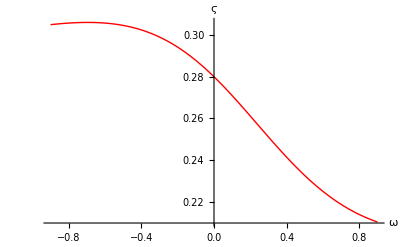

```mathematica
AppendTo[ϛPlotTiming,{"CVApprox",First[Timing[Print[
ϛPlotCVApprox = Plot[ϛOptCVApprox[𝓇1, 𝓇2, 𝓍, Σ, ω, ρ],{ω,ωMinPlot,ωMaxPlot}
,PlotStyle->Red
,AxesLabel->{"ω","ϛ"}
]]]]}];
ϛVals=Transpose[First@Cases[ϛPlotCVApprox,Line[x_]:>x,Infinity]][[2]];
{ϛMin,ϛMax}={Min[ϛMin,Min[ϛVals]],Max[ϛMax,Max[ϛVals]]};
```

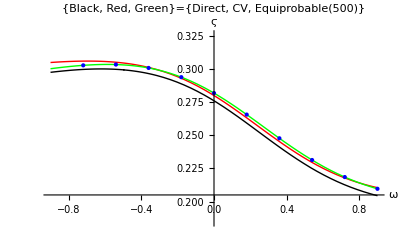

```mathematica
Print[Show[ϛPlotDirect,ϛPlotCVApprox,ϛPlotEqui,ϛPlotEquiList
,PlotLabel->Style["{Black, Red, Green}={Direct, CV, Equiprobable("<>ToString[NumOfPoints]<>")}",14,Black]
,PlotRange->{Automatic,{ϛMin-0.01,ϛMax+0.01}}]];
```

```mathematica
Print[MatrixForm[ϛPlotTiming,TableHeadings->{None,"Method","Seconds"}]];
```

(EquiprobableList | 0.578306
Equiprobable | 17.3155
CVApprox | 0.00935
Direct | 4333.14)